# Stochastic Differential Equations with Mathematica

## About the author

Author : Nelson Mok
email : madeinquant@gmail.com

### Summary

The Mathematica versions in Higham “An Algorithmic Introduction to Numerical Simulation of Stochastic Differential Equations”, SIAM Review, Vol. 43, No. 3, 2001.

The Details can be found in the paper (http://www.caam.rice.edu/~cox/stoch/dhigham.pdf)

## standard Wiener process, looping & vector ( bpath1.m & bpath2.m)

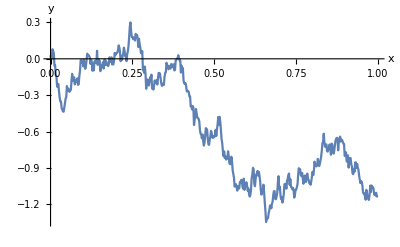
-Graphics-tW(t)

```mathematica
start = 0.0;
T = 1.0;
steps = 500;
dt = T / steps;
t = Range[start,T-dt,dt];
W = Table[0.0,steps];
dW = Table[0.0,steps];

(* 
dW[[1]] = RandomReal[NormalDistribution[0,1]];
W[[1]] = dW[[1]];

For[j=2,j<steps+1,j++,
dW[[j]] = Sqrt[dt] * RandomReal[NormalDistribution[0,1]];
W[[j]] = W[[j-1]] + dW[[j]]
];
*)

dW = Sqrt[dt] * RandomReal[NormalDistribution[0,1],steps];
W = Accumulate[dW];

ts = TimeSeries[W,{t}];
(* ListLinePlot[ts]*)

Labeled[ListLinePlot[ts,AxesLabel->{"x","y"}],{"t","W(t)"},{Bottom,Left},RotateLabel->True]
```

## bpath3

```mathematica
start = 0.0;
T = 1.0;
steps = 5;
dt = T / steps;
t = Range[start,T-dt,dt];

M = 10;

dW = Sqrt[dt] * RandomReal[NormalDistribution[0,1],{M,steps}];
W={};

For[i=1,i< M+1,i++,
W= AppendTo[W,Accumulate[dW[[i]]]] 
]

(*
U = MatrixExp[t+0.5*W];
UMean = Mean[U];

ts = TimeSeries[W,{t}];

Labeled[ListLinePlot[ts,AxesLabel->{"x","y"}],{"t","W(t)"},{Bottom,Left},RotateLabel->True]
*)
```